# Testing Wada property example

First we import the WadaMergingMethod Package, and the basins

```mathematica
Needs["WadaMergingMethod`"];
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\NewBasins

```mathematica
files=FileNames["*e(12)pl500.mx"]
```

{b(01)e(12)pl500.mx,b(02)e(12)pl500.mx,b(03)e(12)pl500.mx,b(04)e(12)pl500.mx,b(05)e(12)pl500.mx,b(06)e(12)pl500.mx,b(07)e(12)pl500.mx}

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black,5-> Purple,6-> Orange,7->Green,8->Gray}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0],5→RGBColor[0.5, 0, 0.5],6→RGBColor[1, 0.5, 0],7→RGBColor[0, 1, 0],8→GrayLevel[0.5]}

```mathematica
mergedColors1={0->White,1->Yellow,2-> Blue,3->Red,4-> Purple,5-> Orange,6->Green};
```

```mathematica
boundColors={0->White,1->Black}
```

{0→GrayLevel[1],1→GrayLevel[0]}

```mathematica
basins=Import[#]&/@files;
```

```mathematica
GraphicsRow[Table[MatrixPlot[basins⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors,ImageSize->400],{i,5}]]
```

-Graphics-

```mathematica
mergedBasins1=getMergedBasins[basins⟦1⟧];
```

```mathematica
origBasinplot=MatrixPlot[basins⟦1⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors];
```

```mathematica
mBasinplot1=MatrixPlot[mergedBasins1⟦1⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->mergedColors1];
mBasinplot2=MatrixPlot[mergedBasins1⟦2⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->mergedColors1];
mBasinplot3=MatrixPlot[mergedBasins1⟦3⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->mergedColors1];
```

```mathematica
GraphicsRow[Table[MatrixPlot[mergedBasins1⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->mergedColors1,ImageSize->400],{i,3}]]
```

-Graphics-

```mathematica
slimBoundaries1=getSlimBoundaries[basins⟦1⟧];
```

```mathematica
GraphicsRow[Table[MatrixPlot[slimBoundaries1⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->boundColors,ImageSize->400],{i,3}]]
```

-Graphics-

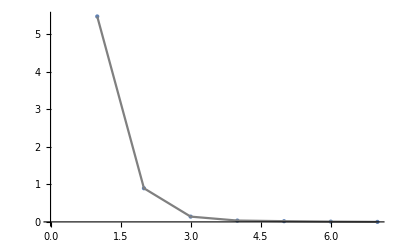

```mathematica
wadaData1=testWada[basins⟦1⟧,20]
```

```mathematica
{{1,4012},{2,657},{3,103},{4,26},{5,14},{6,5},{7,0}} (*Number of pixels remaining that is not classified as Wada at a certain r value*)
```

## Merged basins figure

```mathematica
GraphicsGrid[{{origBasinplot,mBasinplot1},{mBasinplot2,mBasinplot3}}]
```

-Graphics-